# DYS HW4-2 Stability Exponents for a toy model

-Graphics-

## a.) Calculate radius r_0 and the period of the limit cycle for mu > 0

-Graphics-

## b.) Make a phase portrait of the dynamical system (2), showing a few representative trajectories. In the same figure, plot the limit cycle using a suitable representative trajectory. Upload your figure as .pdf or .png. Using StreamPlot]] is not acceptable. (0.5 points)

-Graphics-

-Graphics-

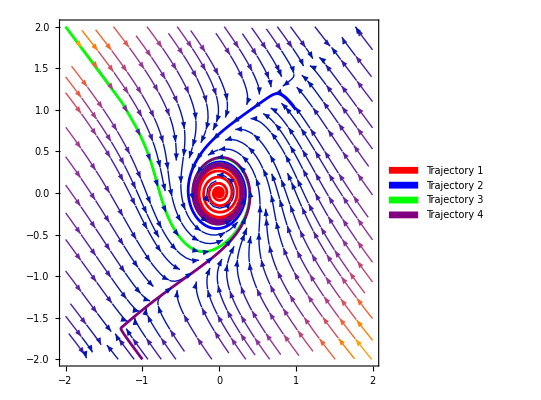

```mathematica
ClearAll["Global`*"]
X1prime = m * X1 - X1^3 - X1 * X2^2 - w * X2 + n * X1^2 * X2 + n * X2^3;
X2prime = m * X2 - X1^2 * X2 - X2^3 + w * X1 + n * X1^3 + n * X2^2 * X1;

m = 0.1; 
w = 1;
n = 1;

system = {
  X1'[t] == m*X1[t] - X1[t]^3 - X1[t]*X2[t]^2 - w*X2[t] + n*X1[t]^2*X2[t] + n*X2[t]^3,
  X2'[t] == m*X2[t] - X1[t]^2*X2[t] - X2[t]^3 + w*X1[t] + n*X1[t]^3 + n*X2[t]^2*X1[t]
};

FP1 = {0,0};
FP2 = {1,1};
FP3 = {-2, 2};
FP4 = {-1,-2};
delta = 0.001;
startingPoint1 = FP1 + delta;
startingPoint2 = FP2;
startingPoint3 = FP3;
startingPoint4 = FP4;

initialConditions1 = {X1[0] == startingPoint1[[1]], X2[0] == startingPoint1[[2]]};
initialConditions2 = {X1[0] == startingPoint2[[1]], X2[0] == startingPoint2[[2]]};
initialConditions3 = {X1[0] == startingPoint3[[1]], X2[0] == startingPoint3[[2]]};
initialConditions4 = {X1[0] == startingPoint4[[1]], X2[0] == startingPoint4[[2]]};


solution1 = NDSolve[{system, initialConditions1}, {X1, X2}, {t, 0, 200}];
solution2 = NDSolve[{system, initialConditions2}, {X1, X2}, {t, 0, 200}];
solution3 = NDSolve[{system, initialConditions3}, {X1, X2}, {t, 0, 200}];
solution4 = NDSolve[{system, initialConditions4}, {X1, X2}, {t, 0, 200}];


Clear[plotWithArrowsWithLegend]

plotWithArrowsWithLegend[solution_, color_, label_] := 
 Module[{trajectory, arrows},
  trajectory = ParametricPlot[Evaluate[{X1[t], X2[t]} /. solution], {t, 0, 200},
    AspectRatio -> 1, PlotRange -> All, AxesLabel -> {"X1", "X2"},
    PlotStyle -> Directive[color, Thickness[0.005]],
    PlotLabel -> label];

  arrows = Table[Arrow[{{X1[t], X2[t]} /. solution, {X1[t + 1], X2[t + 1]} /. solution}], {t, 0, 199}];

  Show[trajectory, Graphics[{Arrowheads[Medium], arrows}]]
]

SP = StreamPlot[{X1prime, X2prime}, {X1,-2,2},{X2,-2,2}];

(* Example usage with legend *)
PP1 = plotWithArrowsWithLegend[solution1, Red, "Trajectory 1"];
PP2 = plotWithArrowsWithLegend[solution2, Blue, "Trajectory 2"];
PP3 = plotWithArrowsWithLegend[solution3, Green, "Trajectory 3"];
PP4 = plotWithArrowsWithLegend[solution4, Purple, "Trajectory 4"];

legend = SwatchLegend[{Red, Blue, Green, Purple}, {"Trajectory 1", "Trajectory 2", "Trajectory 3", "Trajectory 4"}];

Show[SP, Legended[Show[PP1, PP2, PP3, PP4], legend]]
```

## c.) Polar to Cartesian and compare with system 2

Done by hand:

## d.) Plot M and X1, X2 quantities

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

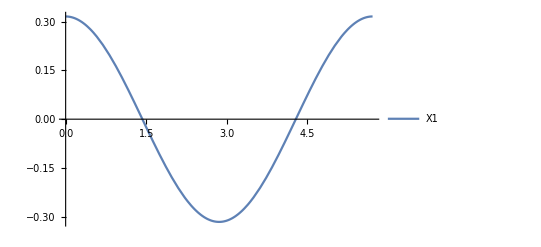

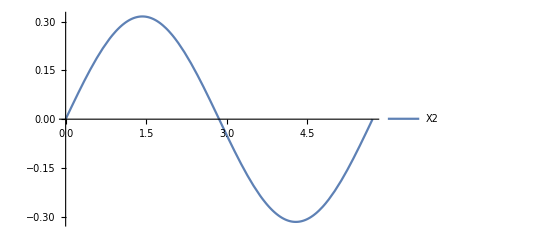

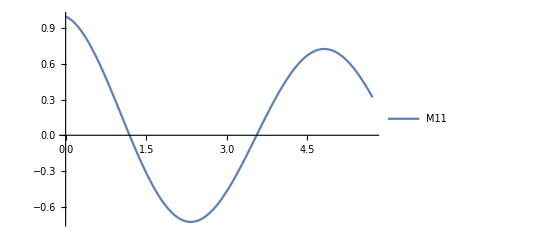

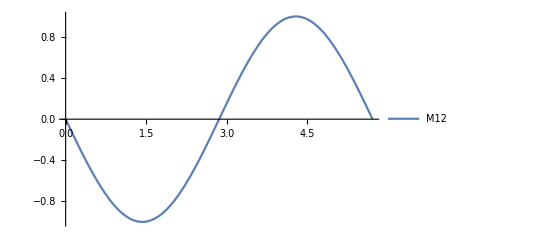

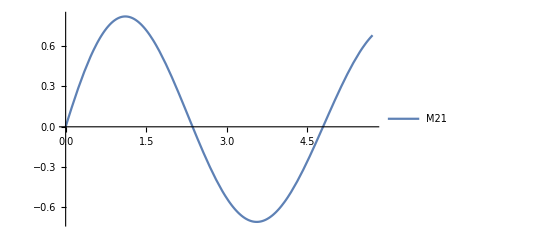

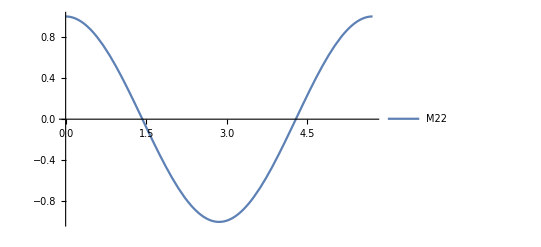

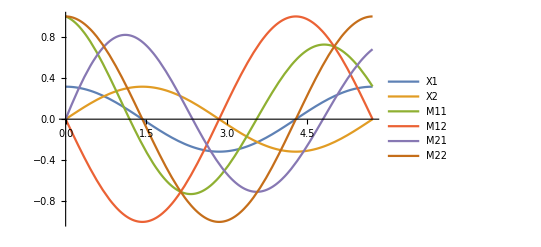

5.71199

Numerical values at T =5.71199

X1:0.316228

X2:-5.21206×10^-9

M11:0.319053

M12:1.6482×10^-8

M21:0.680947

M22:1.

```mathematica
ClearAll["Global`*"]

(* Define the system of differential equations *)
X1prime[X1_, X2_] := 
    0.1 * X1 - X2^3 - X1*(X2^2) - (X1^2) * X2 - X2 - X1^3;
X2prime[X1_, X2_] := 
	X1 + 0.1 * X2 + X1 * (X2^2) + X1^3 - X2^3 - (X1^2) * X2;
w = 1;
nu = 1;
mu = 0.1;
PeriodTime = (2 * Pi)/(w + nu * mu);
t0 = 0;
(*tMax = 20;*)
tMax = PeriodTime;

(* Define the Jacobian matrix *)
J[X1_, X2_] := {{D[X1prime[X1, X2], X1], D[X1prime[X1, X2], X2]},
				{D[X2prime[X1, X2], X1],D[X2prime[X1, X2], X2]}}

J[X1,X2] // MatrixForm;

(* Define the system of differential equations for M' = M * J *)
M11prime[X1_, X2_, M11_, M21_] := J[X1, X2][[1,1]] * M11 + J[X1, X2][[1,2]] * M21;
M12prime[X1_, X2_, M12_, M22_] := J[X1, X2][[1,1]] * M12 + J[X1, X2][[1,2]] * M22;
M21prime[X1_, X2_, M11_, M21_] := J[X1, X2][[2,1]] * M11 + J[X1, X2][[2,2]] * M21;
M22prime[X1_, X2_, M12_, M22_] := J[X1, X2][[2,1]] * M12 + J[X1, X2][[2,2]] * M22;

(* Set the initial conditions *)
initialConditions = {X1[t0] == Sqrt[mu], X2[t0] == 0, M11[t0] == 1, M12[t0] == 0, M21[t0] == 0, M22[t0] == 1};

(* Solve the system of differential equations *)
solution = NDSolve[{
   X1'[t] == X1prime[X1[t], X2[t]],
   X2'[t] == X2prime[X1[t], X2[t]],
   M11'[t] == M11prime[X1[t], X2[t], M11[t], M21[t]],
   M12'[t] == M12prime[X1[t], X2[t], M12[t], M22[t]],
   M21'[t] == M21prime[X1[t], X2[t], M11[t], M21[t]],
   M22'[t] == M22prime[X1[t], X2[t], M12[t], M22[t]],
   initialConditions
   }, {X1, X2, M11, M12, M21, M22}, {t, t0, tMax}, MaxStepSize->0.001];
   
(* Plot individual *)
P11 = Plot[Evaluate[{X1[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"X1"}]
P12 = Plot[Evaluate[{X2[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"X2"}]
PM11 = Plot[Evaluate[{M11[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"M11"}]
PM12 = Plot[Evaluate[{M12[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"M12"}]
PM21 = Plot[Evaluate[{M21[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"M21"}]
PM22 = Plot[Evaluate[{M22[t]/. solution}], {t, t0, tMax}, 
  PlotLegends -> {"M22"}]
(* Plot the solutions *)
Plot[Evaluate[{X1[t], X2[t], M11[t], M12[t], M21[t], M22[t]} /. solution], {t, t0, tMax}, 
  PlotLegends -> {"X1", "X2", "M11", "M12", "M21", "M22"}]
  
(* Print the numerical values at timestep T = tMax *)
tPeriod = PeriodTime
valuesAtTMax = {X1[tPeriod], X2[tPeriod], M11[tPeriod], M12[tPeriod], M21[tPeriod], M22[tPeriod]} /. solution[[1]];

(* Print the values *)
Print["Numerical values at T =", tMax];
Print["X1:", valuesAtTMax[[1]]];
Print["X2:", valuesAtTMax[[2]]];
Print["M11:", valuesAtTMax[[3]]];
Print["M12:", valuesAtTMax[[4]]];
Print["M21:", valuesAtTMax[[5]]];
Print["M22:", valuesAtTMax[[6]]];
```

## f) Calculate the stability exponents of separations simga~1 and sigma~2 of the limit cycle from the eigenvalues of M(T) to 4 relevant digits accuracy. Write your result as the ordered vector [simga~1, simga~2] with simga~1 ≤ simga~2. (0.5 points)

```mathematica
M = {{M11[tPeriod], M12[tPeriod]}, {M21[tPeriod], M22[tPeriod]}} /. solution

sigmas = Log[Eigenvalues[M]]
sigmas = sigmas / tPeriod
```

{{{0.319053,1.6482×10^-8},{0.680947,1.}}}

{8.89036×10^-9,-1.1424}

{1.55644×10^-9,-0.2}

## g) Using what you know from all parts of this problem, calculate the deformation matrix M(T) analytically. Write your exact result (in Cartesian coordinates) in the form [[M11, M121, M21, M22]]. Write exponentials as exp(). (1 point)

```mathematica
(*ClearAll["Global`*"]

(* Define variables and matrices *)
t = Symbol["t"];
X1prime[X1_, X2_] := 
    0.1 * X1 - X2^3 - X1*(X2^2) - (X1^2) * X2 - X2 - X1^3;
X2prime[X1_, X2_] := 
	X1 + 0.1 * X2 + X1 * (X2^2) + X1^3 - X2^3 - (X1^2) * X2;

J[X1_, X2_] := {{D[X1prime[X1, X2], X1], D[X1prime[X1, X2], X2]},
                {D[X2prime[X1, X2], X1], D[X2prime[X1, X2], X2]}};

M0 = {{1,0},{0,1}}
Mt = M0 * ExpM
*)
(*ClearAll["Global`*"]

(* Define variables and matrices *)
X1prime[X1_, X2_, t_] := 
    0.1 * X1[t] - X2[t]^3 - X1[t]*(X2[t]^2) - (X1[t]^2) * X2[t] - X2[t] - X1[t]^3;
X2prime[X1_, X2_, t_] := 
	X1[t] + 0.1 * X2[t] + X1[t] * (X2[t]^2) + X1[t]^3 - X2[t]^3 - (X1[t]^2) * X2[t];

J[X1_, X2_, t_] := {{D[X1prime[X1, X2, t], X1], D[X1prime[X1, X2, t], X2]},
                {D[X2prime[X1, X2, t], X1], D[X2prime[X1, X2, t], X2]}};


(* Define initial condition matrix *)
M0 = {{1, 0}, {0, 1}};

(* Define matrix exponential *)
M[t_] := MatrixExp[J[X1, X2, t] t];

(* Compute M *)
M[(T)] * M0 // MatrixForm // Simplify
*)
```

{{0.1-3 X1^2-2 X1 X2-X2^2,-1-X1^2-2 X1 X2-3 X2^2},{1+3 X1^2-2 X1 X2+X2^2,0.1-X1^2+2 X1 X2-3 X2^2}}

((ⅇ^(-0.5 T (-0.2+4. X1^2+4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (1. X1^2+2. X1 X2-1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))+ⅇ^(0.5 T (0.2-4. X1^2-4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (-1. X1^2-2. X1 X2+1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))/(√(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))) | 0
0 | (ⅇ^(0.5 T (0.2-4. X1^2-4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (1. X1^2+2. X1 X2-1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))+ⅇ^(-0.5 T (-0.2+4. X1^2+4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (-1. X1^2-2. X1 X2+1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))/(√(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))

((ⅇ^(-0.5 T (-0.2+4. X1^2+4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (1. X1^2+2. X1 X2-1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))+ⅇ^(0.5 T (0.2-4. X1^2-4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (-1. X1^2-2. X1 X2+1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))/(√(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))) | 0
0 | (ⅇ^(0.5 T (0.2-4. X1^2-4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (1. X1^2+2. X1 X2-1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))+ⅇ^(-0.5 T (-0.2+4. X1^2+4. X2^2+1. √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2)))) (-1. X1^2-2. X1 X2+1. X2^2+0.5 √(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))/(√(-4.-8. X1^4-16. X2^2-8. X2^4+X1^2 (-16.-16. X2^2))))

```mathematica
ClearAll["Global`*"]

tPeriod = 2*Pi/1.1;

Jpol = {{m - 3 * r^2, 0}, {2 * n * r, 0}};
M0 = {{1,0},{0,1}};
Mpolar = M0.MatrixExp[Jpol*t];

r[X1_, X2_] := Sqrt[X1^2 + X2^2];
phi[X1_, X2_] := ArcTan[X1, X2];

Jpol2cart = {{D[r[X1,X2], X1], D[r[X1,X2], X2]},{D[phi[X1,X2], X1], D[phi[X1,X2], X2]}};
Jpol2CartInv = Inverse[Jpol2cart];

Mcart = Jpol2CartInv . Mpolar . Jpol2cart // Simplify;
Mcart1 = Mcart /. r->(Sqrt[X1^2 + X2^2]) // Simplify;
m = 0.1;
n = 1;
t = tPeriod;
X1 = Sqrt[0.1];
X2 = 0;
Mcart1 // Simplify // MatrixForm

Eigenvalues[Mcart1] // Simplify;
```

(0.319053 | 0.
0.680947 | 1.)